{-0.2 t x[t]+x''[t]==0}

{x[0]==1,x'[0]==0}

{{x→InterpolatingFunction[…]}}

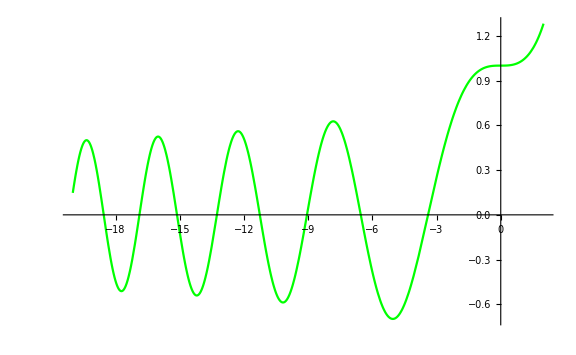

```mathematica
s={x''[t]-0.2t*x[t]==0}
ics={x[0]== 1,x'[0]==- 0}
sol=NDSolve[{s,ics},{x},{t,-20,2}]
Plot[Evaluate[x[t]/.sol],{t,-20,2},PlotRange->All,PlotStyle->Green,ImageSize->Large]
```